Exercises for Section 28 | Tests and Conditionals

Test whether 123^321 is greater than 456^123. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
123^(321)>456^(123)
```

True

Get a list of numbers up to 100 whose digits add up to less than 5. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
FromDigits/@Select[IntegerDigits@ Range[100],Total[#]<5&]
```

{1,2,3,4,10,11,12,13,20,21,22,30,31,40,100}

Make a list of the first 20 integers, with prime numbers styled red. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
If[PrimeQ[#],Style[#,Red],#]&/@Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Find words in WordList[ ] that both begin and end with the letter “p”. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Select[WordList[], StringTake[#, 1] == StringTake[#, -1] == "p" &]
```

{pap,paperclip,parsnip,partisanship,partnership,pawnshop,peep,penmanship,pep,pickup,pileup,pip,plop,plump,polyp,pomp,pop,premiership,prep,primp,professorship,prop,proprietorship,pulp,pump,pup}

Make a list of the first 100 primes, keeping only ones whose last digit is less than 3. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Select[IntegerDigits[Select[Range[100],PrimeQ[#]&]],Take[#,-1]<3]
```

{}

```mathematica
Take[{{11},{22}},1]
```

{{11}}

```mathematica
Select[Array[Prime, 100], Last[IntegerDigits[#]] < 3 &]
```

{2,11,31,41,61,71,101,131,151,181,191,211,241,251,271,281,311,331,401,421,431,461,491,521,541}

Find Roman numerals up to 100 that do not contain “I”. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
RomanNumeral/@Select[Range[100],!MemberQ[IntegerDigits[#],1]&]
```

{II,III,IV,V,VI,VII,VIII,IX,XX,XXII,XXIII,XXIV,XXV,XXVI,XXVII,XXVIII,XXIX,XXX,XXXII,XXXIII,XXXIV,XXXV,XXXVI,XXXVII,XXXVIII,XXXIX,XL,XLII,XLIII,XLIV,XLV,XLVI,XLVII,XLVIII,XLIX,L,LII,LIII,LIV,LV,LVI,LVII,LVIII,LIX,LX,LXII,LXIII,LXIV,LXV,LXVI,LXVII,LXVIII,LXIX,LXX,LXXII,LXXIII,LXXIV,LXXV,LXXVI,LXXVII,LXXVIII,LXXIX,LXXX,LXXXII,LXXXIII,LXXXIV,LXXXV,LXXXVI,LXXXVII,LXXXVIII,LXXXIX,XC,XCII,XCIII,XCIV,XCV,XCVI,XCVII,XCVIII,XCIX}

```mathematica
Select[RomanNumeral /@ Range[100], ! MemberQ[Characters[#], "I"] &]
```

{V,X,XV,XX,XXV,XXX,XXXV,XL,XLV,L,LV,LX,LXV,LXX,LXXV,LXXX,LXXXV,XC,XCV,C}

Get a list of Roman numerals up to 1000 that are palindromes. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Select[RomanNumeral /@ Range[1000], PalindromeQ]
```

{I,II,III,V,X,XIX,XX,XXX,L,C,CXC,CC,CCC,D,M}

Find names of integers up to 100 that begin and end with the same letter. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Select[Table[IntegerName[n], {n, 100}], 
 First@Characters[#] == Last@Characters[#] &]
```

{nineteen,twenty-eight,thirty-eight,eighty-one,eighty-three,eighty-five,eighty-nine,ninety-seven}

Get a list of words longer than 15 characters from the Wikipedia article on words. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Select[TextWords[WikipediaData["words"]], StringLength[#] > 15 &]
```

{Definitions/meanings,orthographically,multiple-morpheme,lavarse.Japanese,Proto-Indo-European,978-0-19-924370-9,978-0-521-28492-9,978-0-521-40179-1,978-0-415-23377-4,978-0-415-29893-3,978-0-521-52563-3,978-0-19-870002-9}

Starting from 1000, divide by 2 if the number is even, and compute 3#+1& if the number is odd; do this repeatedly 200 times (Collatz problem). |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
NestList[If[EvenQ[#] ,#/2,3 #+1] & ,1000,200]
```

{1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2}

Make a word cloud of 5-letter words in the Wikipedia article on computers. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

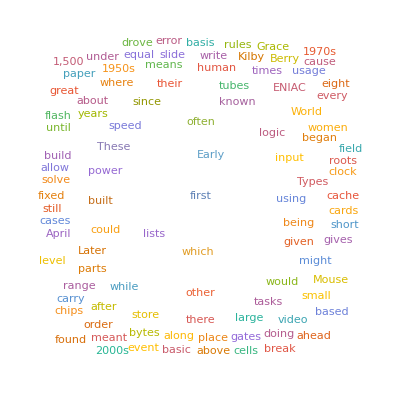

```mathematica
WordCloud@Select[TextWords[WikipediaData["computers"]],StringLength[#]==5&]
```

Find words in WordList[ ] whose first 3 letters are the same as their last 3 read backward, but where the whole string is not a palindrome. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Select[WordList[],Take[#,3]&&Reverse[Take[#,-3]]&]
```

Take::normal: Nonatomic expression expected at position 1 in Take[a,3].

Take::normal: Nonatomic expression expected at position 1 in Take[a,-3].

Take::normal: Nonatomic expression expected at position 1 in Take[-3,a].

General::stop: Further output of Take::normal will be suppressed during this calculation.

{}

```mathematica
For[
i=1,i=1000,i++,
Print[Take[WordList[],i]]
]
```

```mathematica
Select[WordList[], 
 StringLength[#] >= 3 && 
   StringTake[#, 3] == StringTake[StringReverse[#], 3] && # != 
    StringReverse[#] &]
```

{despised,detected,detested,drainboard,foolproof,lackadaisical,marjoram,revolver}

Find all 10-letter words in WordList[ ] for which the total of LetterNumber values is 100. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Select[Select[WordList[],StringLength[#]==10&],Total[LetterNumber[Characters[#]]]==100&]
```

{accumulate,alienation,answerable,apoplectic,aquamarine,bewitching,censurable,ceramicist,chastening,chimpanzee,clinically,collecting,condensate,congenital,conjugated,connivance,declension,deliquesce,demobilize,demodulate,denominate,diagonally,discipline,discommode,egoistical,emasculate,embodiment,emendation,empathetic,fatalistic,fatherhood,geographer,hemoglobin,inadequacy,interbreed,leveraging,liberalism,likelihood,martingale,mercantile,meridional,neoclassic,paramecium,plebiscite,potbellied,quadrangle,reciprocal,regimented,reschedule,researcher,scoreboard,septicemia,shibboleth,sleepyhead,stagecraft,stalemated,temperance,thickening,threatened,uncombined,unmodified}

Make a table of integers up to 25 where every integer ending in 3 is replaced with 0. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
If[Range[25]=2,x,y]
```

Set::write: Tag Range in Range[25] is Protected.

If[2,x,y]

```mathematica
Select[If[Last[IntegerDigits[#]] == 3, #, a] & /@ Range[25], NumberQ]
```

{3,13,23}

```mathematica
If[Last[IntegerDigits[#]] == 3, 0, #] & /@ Range[25]
```

{1,2,0,4,5,6,7,8,9,10,11,12,0,14,15,16,17,18,19,20,21,22,0,24,25}

Use Table and If to make a 5×5 array that is 1 on its leading diagonal, and 0 otherwise.  |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Grid@Array[f,{5,5}]
```

f[1,1] | f[1,2] | f[1,3] | f[1,4] | f[1,5]
f[2,1] | f[2,2] | f[2,3] | f[2,4] | f[2,5]
f[3,1] | f[3,2] | f[3,3] | f[3,4] | f[3,5]
f[4,1] | f[4,2] | f[4,3] | f[4,4] | f[4,5]
f[5,1] | f[5,2] | f[5,3] | f[5,4] | f[5,5]

```mathematica
Table[Table[If[First[#]],5],5]
```

{{x,x,x,x,x},{x,x,x,x,x},{x,x,x,x,x},{x,x,x,x,x},{x,x,x,x,x}}

```mathematica
Table[If[First[#]==1,x]&,5]
```

{If[First[#1]==1,x]&,If[First[#1]==1,x]&,If[First[#1]==1,x]&,If[First[#1]==1,x]&,If[First[#1]==1,x]&}

```mathematica
If[First[#]==x,1]/@Table[x,5]
```

{If[1==x,1][x],If[1==x,1][x],If[1==x,1][x],If[1==x,1][x],If[1==x,1][x]}

```mathematica
Table[Table[If[i==j,1,0],{i,5}],{j,5}]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
Table[Table[If[i==j,1,0],{j,5}],{i,5}]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

Get a list of numbers up to 1000 that are equal to 1 mod both 7 and 8. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Select[Range[1000],Mod[#,7]==Mod[#,8]==1&]
```

{1,57,113,169,225,281,337,393,449,505,561,617,673,729,785,841,897,953}

Make a list of numbers up to 100, where multiples of 3 are replaced by Black, multiples of 5 by White and multiples of 3 and 5 by Red. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
If[Mod[#,3]==0,Black,#]&/@Range[100]
```

{1,2,GrayLevel[0],4,5,GrayLevel[0],7,8,GrayLevel[0],10,11,GrayLevel[0],13,14,GrayLevel[0],16,17,GrayLevel[0],19,20,GrayLevel[0],22,23,GrayLevel[0],25,26,GrayLevel[0],28,29,GrayLevel[0],31,32,GrayLevel[0],34,35,GrayLevel[0],37,38,GrayLevel[0],40,41,GrayLevel[0],43,44,GrayLevel[0],46,47,GrayLevel[0],49,50,GrayLevel[0],52,53,GrayLevel[0],55,56,GrayLevel[0],58,59,GrayLevel[0],61,62,GrayLevel[0],64,65,GrayLevel[0],67,68,GrayLevel[0],70,71,GrayLevel[0],73,74,GrayLevel[0],76,77,GrayLevel[0],79,80,GrayLevel[0],82,83,GrayLevel[0],85,86,GrayLevel[0],88,89,GrayLevel[0],91,92,GrayLevel[0],94,95,GrayLevel[0],97,98,GrayLevel[0],100}

```mathematica
Table[If[Mod[i,3]==Mod[i,5]==0,Red,If[Mod[i,3],Black]],{i,100}]

Table[If[Mod[n, 3] == Mod[n, 5] == 0, Red, 
  If[Mod[n, 5] == 0, White, If[Mod[n, 3] == 0, Black, n]],i], {n, 100}]
```

{If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],RGBColor[1, 0, 0],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],RGBColor[1, 0, 0],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],RGBColor[1, 0, 0],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],RGBColor[1, 0, 0],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],RGBColor[1, 0, 0],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],RGBColor[1, 0, 0],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black],If[2,Black],If[0,Black],If[1,Black]}

{1,2,GrayLevel[0],4,GrayLevel[1],GrayLevel[0],7,8,GrayLevel[0],GrayLevel[1],11,GrayLevel[0],13,14,RGBColor[1, 0, 0],16,17,GrayLevel[0],19,GrayLevel[1],GrayLevel[0],22,23,GrayLevel[0],GrayLevel[1],26,GrayLevel[0],28,29,RGBColor[1, 0, 0],31,32,GrayLevel[0],34,GrayLevel[1],GrayLevel[0],37,38,GrayLevel[0],GrayLevel[1],41,GrayLevel[0],43,44,RGBColor[1, 0, 0],46,47,GrayLevel[0],49,GrayLevel[1],GrayLevel[0],52,53,GrayLevel[0],GrayLevel[1],56,GrayLevel[0],58,59,RGBColor[1, 0, 0],61,62,GrayLevel[0],64,GrayLevel[1],GrayLevel[0],67,68,GrayLevel[0],GrayLevel[1],71,GrayLevel[0],73,74,RGBColor[1, 0, 0],76,77,GrayLevel[0],79,GrayLevel[1],GrayLevel[0],82,83,GrayLevel[0],GrayLevel[1],86,GrayLevel[0],88,89,RGBColor[1, 0, 0],91,92,GrayLevel[0],94,GrayLevel[1],GrayLevel[0],97,98,GrayLevel[0],GrayLevel[1]}

```mathematica
Table[If[Mod[n, 3] == Mod[n, 5] == 0, Red, 
  If[Mod[n, 3] == 0, Black, If[Mod[n, 5] == 0, White, n]]], {n, 100}]
```

{1,2,GrayLevel[0],4,GrayLevel[1],GrayLevel[0],7,8,GrayLevel[0],GrayLevel[1],11,GrayLevel[0],13,14,RGBColor[1, 0, 0],16,17,GrayLevel[0],19,GrayLevel[1],GrayLevel[0],22,23,GrayLevel[0],GrayLevel[1],26,GrayLevel[0],28,29,RGBColor[1, 0, 0],31,32,GrayLevel[0],34,GrayLevel[1],GrayLevel[0],37,38,GrayLevel[0],GrayLevel[1],41,GrayLevel[0],43,44,RGBColor[1, 0, 0],46,47,GrayLevel[0],49,GrayLevel[1],GrayLevel[0],52,53,GrayLevel[0],GrayLevel[1],56,GrayLevel[0],58,59,RGBColor[1, 0, 0],61,62,GrayLevel[0],64,GrayLevel[1],GrayLevel[0],67,68,GrayLevel[0],GrayLevel[1],71,GrayLevel[0],73,74,RGBColor[1, 0, 0],76,77,GrayLevel[0],79,GrayLevel[1],GrayLevel[0],82,83,GrayLevel[0],GrayLevel[1],86,GrayLevel[0],88,89,RGBColor[1, 0, 0],91,92,GrayLevel[0],94,GrayLevel[1],GrayLevel[0],97,98,GrayLevel[0],GrayLevel[1]}

Use Select to get a list of planets whose mass is larger than Earth. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Select[EntityList[EntityClass["Planet",All]],#["Mass"]>Entity["Planet","Earth"]["Mass"]&]
```

{Jupiter,Saturn,Uranus,Neptune}

Make a 50×50 array plot in which a square at position i,j is black if Mod[i,j]==0. |

EXPECTED OUTPUT »

-Graphics- | ×

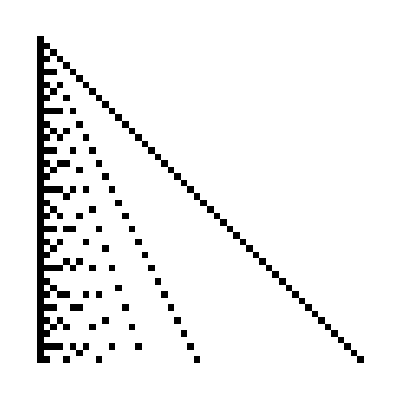

```mathematica
ArrayPlot@Table[Table[If[Mod[i,j]==0,Black,0],{j,50}],{i,50}]
```

Make a 100×100 array plot in which a square is black if the values of both its x and y positions do not contain a 5. |

EXPECTED OUTPUT »

-Graphics- | ×

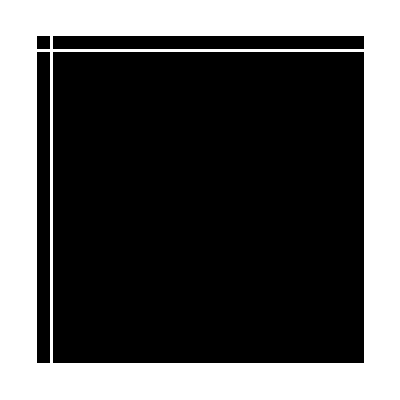

-Graphics-

```mathematica
ArrayPlot@Table[Table[If[i≠5&&j≠5,Black,0],{j,100}],{i,100}]
ArrayPlot[Table[If[!MemberQ[IntegerDigits[y],5]&&!MemberQ[IntegerDigits[x],5],1,0],{x,100},{y,100}]]
```

```mathematica
ArrayPlot[Table[If[!MemberQ[IntegerDigits[y],5]&&!MemberQ[IntegerDigits[x],5],1,0],{x,100},{y,100}]]
```

-Graphics-